```mathematica
meas[100] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\100.2.csv","CSV"]];
meas[200] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\200.2.csv","CSV"]];
meas[300] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\300.2.csv","CSV"]];
meas[400] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\400.2.csv","CSV"]];
meas[500] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\500.2.csv","CSV"]];
meas[600] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\600.2.csv","CSV"]];
meas[700] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\700.2.csv","CSV"]];
meas[800] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\800.2.csv","CSV"]];
meas[900] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\900.2.csv","CSV"]];
meas[1000] = Flatten[Import["\\\\TITAN\\RDProfiles$\\lweaver\\Desktop\\1000.2.csv","CSV"]];
```

### Plot CDF of a single set of measurements

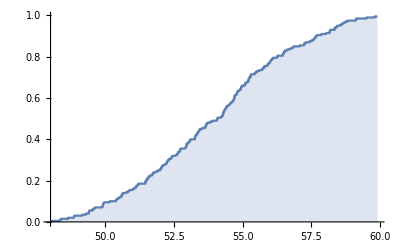

```mathematica
dataset = meas[20];
𝒟=EmpiricalDistribution[dataset];
DiscretePlot[CDF[𝒟,x],{x,Min[dataset],Max[dataset],.001}]
```

### Use many data sets to produce a scatterplot

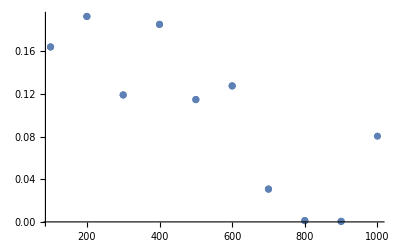

```mathematica
(*Create a table to hold all of the lengths, standard errors*)
maxN = 1000;
points= Table[{Length[meas[i]], StandardDeviation[meas[i]]/Sqrt[Length[meas[i]]]},{i,1,maxN,1}];
ListPlot[points,PlotRange-> All]
```